# Non-Hermitian Fermi-Dirac Distribution in Persistent Current Transport

ABSTRACT (original article): Persistent currents circulate continuously without requiring external power sources. Here, we extend their theory to include dissipation within the framework of non-Hermitian quantum Hamiltonians. Using Green’s function formalism, we introduce a non-Hermitian Fermi-Dirac distribution and derive an analytical expression for the persistent current that relies solely on the complex spectrum. We apply our formula to two dissipative models supporting persistent currents: (i) a phase-biased superconducting-normal-superconducting junction; (ii) a normal ring threaded by a magnetic flux. We show that the persistent currents in both systems exhibit no anomalies at any emergent exceptional points, whose signatures are only discernible in the current susceptibility. We validate our findings by exact diagonalization and extend them to account for finite temperatures and interaction effects. Our formalism offers a general framework for computing quantum many-body observables of non-Hermitian systems in equilibrium, with potential extensions to non-equilibrium scenarios.
CITATION (original article): Pei-Xin Shen, Zhide Lu, Jose Lado, and Mircea Trif, Non-Hermitian Fermi-Dirac Distribution in Persistent Current Transport, Phys. Rev. Lett. 133, 086301 (2024). https://doi.org/10.1103/PhysRevLett.133.086301

# Introduction

This notebook accompanies the Letter titled Non-Hermitian Fermi-Dirac Distribution in Persistent Current Transport and provides a comprehensive exploration of dissipation within the framework of non-Hermitian quantum Hamiltonians. We introduce the non-Hermitian Fermi-Dirac distribution via Green’s function formalism, offering both analytical derivations and numerical verifications to extend the understanding of persistent currents in phase-biased SNS junctions and mesoscopic rings. Beyond supporting the findings of the Letter, this notebook includes detailed derivations, visualizations, and numerical verifications of key concepts, such as the continuity of quantum many-body observables at exceptional points and the construction of non-Hermitian effective Hamiltonians. This notebook serves as a valuable resource for researchers investigating the interplay between dissipation, non-Hermitian dynamics, and quantum transport.

# Non-Hermitian Fermi-Dirac Distribution in Equation (8)

In this chapter, we delve into the detailed derivation, visualization, and asymptotic behavior of the non-Hermitian Fermi-Dirac distribution as formulated in Equation (8) of the accompanying Letter.

## Derivation

The derivation in this section involves detailed analysis of the integrand poles, supported by useful identities, along with contour integration in the complex plane.

Integrand Poles

We begin by analyzing the poles of the integrand in Equation (S14):

```mathematica
Clear["Global`*"];
integrand=1/(Exp[β ω]+1)1/(ω-ε);
FullSimplify@FunctionPoles[integrand,ω]
```

{{ε,1},{ConditionalExpression[(ⅈ (π+2 π C[1]))/β, C[1]∈ℤ],1}}

Useful Identities

Next, we verify some identities used in the derivation of Equation (S15):

```mathematica
FullSimplify[{
Sum[1/(m+z-1),{m,M}]==PolyGamma[M+z]-PolyGamma[z],
PolyGamma[1-z]-PolyGamma[z]==π Cot[π z],
PolyGamma[1/2+ⅈ (β ε)/(2 π)]+PolyGamma[1/2-ⅈ (β ε)/(2 π)]==PolyGamma[1/2+ⅈ (β ε)/(2 π)]+PolyGamma[1-(1/2+ⅈ (β ε)/(2 π))]==2PolyGamma[1/2+ⅈ (β ε)/(2 π)]+π Cot[π (1/2+ⅈ (β ε)/(2 π))],
π Cot[π (1/2+ⅈ (β ε)/(2 π))]==ⅈ π (1/(1+ⅇ^(+β ε))-1/(1+ⅇ^(-β ε)))}]
```

{True,True,True,True}

We also check the identity used in Equation (S23):

```mathematica
FullSimplify[LogGamma[z]+LogGamma[1-z]==Log[π]-Log@Sin[π z]==Log[π Csc[π z]],Assumptions->{0<z<1}]
```

True

Lower Half

We first visualize the integrand in the lower half of the complex plane.

```mathematica
Block[{β=1,R=10,ε=1-ⅈ},
Show[ComplexPlot[integrand,{ω,-R-R ⅈ,+R+R ⅈ},ColorFunction->"MaxAbs"],RegionPlot@Disk[{0,0},R,{π,2π}],ImageSize->Medium]]
```

-Graphics-

The residue of the complex eigenvalue in the lower half of the complex plane is calculated as:

```mathematica
FullSimplify[-2π ⅈ Residue[integrand,{ω,ε}]]
```

-(2 ⅈ π)/(1+ⅇ^(β ε))

Additionally, we calculate the residue of the singularity along the negative imaginary axis as:

```mathematica
FullSimplify@Block[{M=6},
Sum[-2π ⅈ Residue[integrand,{ω,(m-1/2)2π ⅈ/β}],{m,-M+1,0}]==-Sum[(+m-1/2-(ⅈ β ε)/(2π))^-1,{m,1,M}]==-(PolyGamma[+M+1/2-(ⅈ β ε)/(2π)]-PolyGamma[+1/2-(ⅈ β ε)/(2π)])]
```

True

This confirms the equivalence of the sums involving residues and digamma functions.

Upper Half

Similarly, we visualize the integrand in the upper half of the complex plane.

```mathematica
Block[{β=1,R=10,ε=1-ⅈ},
Show[ComplexPlot[integrand,{ω,-R-R ⅈ,+R+R ⅈ},ColorFunction->"MaxAbs"],RegionPlot@Disk[{0,0},R,{0,π}],ImageSize->Medium]]
```

-Graphics-

The residue of the singularity along the positive imaginary axis is calculated as:

```mathematica
FullSimplify@Block[{M=6},
Sum[+2π ⅈ Residue[integrand,{ω,(m-1/2)2π ⅈ/β}],{m,1,+M,1}]==-Sum[(+m-1/2+(ⅈ β ε)/(2π))^-1,{m,1,M}]==-(PolyGamma[+M+1/2+(ⅈ β ε)/(2π)]-PolyGamma[+1/2+(ⅈ β ε)/(2π)])]
```

True

Again, this confirms the validity of the derived expressions with digamma functions.

Average Two Contours

Finally, we obtain the non-Hermitian Fermi-Dirac Distribution in Equation (8) by averaging the residues from both contours.

```mathematica
FullSimplify[1/2(-(2 ⅈ π)/(1+ⅇ^(β ε))+PolyGamma[+1/2+(ⅈ β ε)/(2π)]+PolyGamma[+1/2-(ⅈ β ε)/(2π)])==PolyGamma[+1/2+(ⅈ β ε)/(2π)]-(ⅈ π)/2]
```

True

## Visualization

In this section, we visualize the derived non-Hermitian Fermi-Dirac distribution under different temperature conditions:  and , which corresponds to Figure 3(c) in the main text.

We define the non-Hermitian Fermi-Dirac distribution at zero temperature , and verify that the distribution function is analytic in the lower half of the complex plane.

```mathematica
Clear["Global`*"];
feff[ε_]:=-1/π Log[ε];
FunctionAnalytic[{feff[ε],Im[ε]<0},ε,Complexes]
```

True

We generate a 3D plot that visualizes the imaginary part of the non-Hermitian Fermi-Dirac distribution at zero temperature. The axes represent the real and imaginary parts of the complex energy ε.

```mathematica
Block[{ε=r Exp[ⅈ ϕ]},Show[
Graphics3D[{Arrowheads[0.05],
Arrow[{{0,0,0},{1.2,0,0}}],Text["Re ε",{1.1,-0.2,0}],
Arrow[{{0,0,0},{0,-0.9,0}}],Text["Im ε",{-0.2,-0.8,0}],
Arrow[{{0,0,0},{0,0,1.2}}],Text["Θ(-ϵ)",{0.3,0,0.6}],
Text["-1/πIm[ln(ε)]",{0,0,1.3}],Text["Im[(ε)]",{-0.5,0,0.5}]},
Boxed->False,ViewPoint->{5,-10,5},AspectRatio->2/3,BaseStyle->{FontFamily->"Times",FontSize->24}],
ParametricPlot3D[{Re@ε,Im@ε,Im@feff[ε]},{r,0,1},{ϕ,π,2π},PlotStyle->Opacity[0.5],Mesh->None,ColorFunction->(Hue[#5]&),Axes->False],ParametricPlot3D[{ϵ,0,HeavisideTheta[-ϵ]},{ϵ,-1,1},PlotStyle->{Black,Dashing[0.012],Thickness[0.01]},ExclusionsStyle->{{Black,Dashing[0.015],Thickness[0.01]},Black}],ParametricPlot3D[{x,0,z},{x,-1,1},{z,0,1},Mesh->None,PlotStyle->Directive[Gray,Opacity[0.1]]],ImageSize->350,Method->{"ShrinkWrap"->True}]]
```

-Graphics3D-

We define the non-Hermitian Fermi-Dirac distribution at a finite temperature , and verify the analyticity of the distribution function in the lower half of the complex plane.

```mathematica
Clear["Global`*"];
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
FunctionAnalytic[{feff[ε,β],Im[ε]<0},ε,Complexes,Assumptions->β>0]
```

True

We create a 3D plot to visualize the imaginary part of the non-Hermitian Fermi-Dirac distribution at finite temperature. The axes again represent the real and imaginary parts the complex energy ε.

```mathematica
Block[{β=20,ε=r Exp[ⅈ ϕ]},Show[
Graphics3D[{Arrowheads[0.05],
Arrow[{{0,0,0},{1.2,0,0}}],Text["Re ε",{1.1,-0.2,0}],
Arrow[{{0,0,0},{0,-0.9,0}}],Text["Im ε",{-0.2,-0.8,0}],
Arrow[{{0,0,0},{0,0,1.2}}],Text["",{0.4,0,0.6}],
Text["-1/π",{0.1,0,1.5}],Text["Im[(ε, β)]",{-0.5,0,0.5}]},
Boxed->False,ViewPoint->{5,-10,5},AspectRatio->2/3,BaseStyle->{FontFamily->"Times",FontSize->24}],ParametricPlot3D[{Re@ε,Im@ε,-1/π Im[(PolyGamma[1/2+ⅈ (β ε)/(2 π)]-(ⅈ π)/2)]},{r,0,1},{ϕ,π,2π},PlotStyle->Opacity[0.5],Mesh->None,ColorFunction->(Hue[#5]&),Axes->False],ParametricPlot3D[{ϵ,0,1/(1+Exp[β ϵ])},{ϵ,-1,1},PlotStyle->{Black,Dashing[0.012],Thickness[0.01]}],ParametricPlot3D[{x,0,z},{x,-1,1},{z,0,1},Mesh->None,PlotStyle->Directive[Gray,Opacity[0.1]]],ImageSize->350,Method->{"ShrinkWrap"->True}]]
```

-Graphics3D-

## Asymptotic Behavior

This section explores the asymptotic limits of the non-Hermitian Fermi-Dirac distribution, including the Hermitian limit as the non-Hermitian parameter  approaches zero, as well as the zero and infinite temperature limits. These analyses are crucial for understanding the broader implications of the non-Hermitian formulation in persistent current calculations, as discussed in Section II-C of the supplemental material.

Distribution and Free Energy

We begin by defining the non-Hermitian Fermi-Dirac distribution for both zero and non-zero temperatures. The function  is defined using the log function for  while the poly-gamma function for .

```mathematica
Clear["Global`*"];
feff[ε_]:=-1/π Log[ε];
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
```

Additionally, we define the the log-gamma function in the non-Hermitian free energy , which plays a crucial role in Equation (9) of the main text.

```mathematica
ℱeff[ε_,β_]:=1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]);ℱLogGamma[ε_,β_]:=LogGamma[1/2+(ⅈ β ε)/(2 π)];
```

We also define a symbolic conjugation function 𝒦 to handle the complex conjugate of symbolic expressions.

```mathematica
𝒦[operator_]:=operator/.Complex[x_,y_]:>Complex[x,-y];
```

Hermitian Limit ()

Next, we examine the Hermitian limit of the non-Hermitian Fermi-Dirac distribution as . For  in Equation (S21), the limit is computed as:

```mathematica
Limit[feff[ϵ-ⅈ η],η->0,Assumptions->#,Direction->"FromAbove"]&/@{ϵ<0,ϵ>0}
```

{ⅈ-Log[-ϵ]/π,-Log[ϵ]/π}

For  in Equation (S21), we assume ϵ is real and use the symbolic conjugate 𝒦 to verify the equality.

```mathematica
FullSimplify[feff[ϵ,β]==1/2(feff[ϵ,β]+𝒦@feff[ϵ,β])+1/2(feff[ϵ,β]-𝒦@feff[ϵ,β])==1/2(feff[ϵ,β]+𝒦@feff[ϵ,β])+ⅈ 1/(ⅇ^(β ϵ)+1)]
```

True

Note that we use the following identities to derive the limits for  below Equation (S22).

```mathematica
SeedRandom[0608];
Block[{β=RandomReal@{5,10},ϵ=RandomReal@{-10,10},η=10^-8,ε},ε=ϵ-ⅈ η;Chop[{
ℱeff[ε,β],2/β Re@ℱLogGamma[ε,β],1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]),
1/β(Log[2π]+(β ε)/2-Log[1+ ⅇ^(β ε)]),1/β(Log[2π]-Log[ ⅇ^(+(β ε)/2)+ ⅇ^(-(β ε)/2)])},10^-6]]
```

{-0.923937,-0.923937,-0.923937,-0.923937,-0.923937}

Zero Temperature ()

We proceed by analyzing the asymptotic behavior of the non-Hermitian Fermi-Dirac distribution as the temperature approaches zero, corresponding to  in Equation (S22).

```mathematica
FullSimplify@PowerExpand[Asymptotic[feff[ε,β],{β,∞,2},Assumptions->{β>0,ε>0}]==-1/π(Log[β/(2 π)]+Log[ε]-π^2/(6 β^2 ε^2))]
```

True

Furthermore, the asymptotic expansion of the log-gamma function, referenced below Equation (S23), is evaluated as:

```mathematica
FullSimplify@PowerExpand[Asymptotic[1/β ℱLogGamma[ε,β],{β,∞,3}]==ⅈ/(2 π)(ε Log[ε]+ε Log[(ⅈ β)/(2 π ⅇ)])+Log[2 π]/(2 β)+(ⅈ π)/(12 β^2 ε)]
```

True

Infinite Temperature ()

Finally, we analyze the asymptotic behavior of the non-Hermitian Fermi-Dirac distribution as the temperature approaches infinity, corresponding to  in Equation (S22):

```mathematica
FullSimplify[Normal@Series[feff[ε,β],{β,0,1},Assumptions->{β>0,ε>0}]==-1/π(PolyGamma[1/2] -ⅈ π (1/2-(β ε)/4))]
```

True

The asymptotic expansion of the log-gamma function in the infinite temperature limit, referenced below Equation (S23), is evaluated as:

```mathematica
FullSimplify[Normal@Series[1/β ℱLogGamma[ε,β],{β,0,1}]==Log[π]/(2 β)+(ⅈ PolyGamma[1/2])/(2 π)ε -(β ε^2)/16]
```

True

# Current Continuity at Exceptional Points

In this chapter, we examine the continuity of quantum many-body observables—persistent currents—at exceptional points in non-Hermitian systems. We begin with a toy model to demonstrate the general principles, followed by an in-depth analysis based on the derivations in Section II-D of the Supplemental Material, focusing on the behavior of the non-Hermitian Fermi-Dirac distribution and free energy at both zero and finite temperatures.

## Toy Model

In this section, we provide technical details regarding the continuity of many-body observables for a non-Hermitian toy model at exceptional points, as discussed in the blog titled Quantum many-body observables in equilibrium are continuous at exceptional points.

Biorthogonal Eigensystems

We begin by defining the non-Hermitian 2 by 2 Hamiltonian  and compute its biorthogonal eigensystems:

```mathematica
Clear["Global`*"];
ℋeff=({{0, 1}, {1, -2ⅈ κ}});
{symbolicValsR,symbolicVecsR}=FullSimplify[Reverse[Eigensystem[ℋeff]ᵀ]ᵀ];
{εp,εm}=symbolicValsR
```

{-ⅈ κ+√(1-κ^2),-ⅈ κ-√(1-κ^2)}

The original unnormalized right wavefunctions are

```mathematica
-1/(√2)symbolicVecsR==1/(√2)({{εm, εp}, {-1, -1}})ᵀ//Simplify
```

True

For simplicity, we redefine the right wavefunctions and calculate the corresponding left wavefunctions:

```mathematica
symbolicVecsR=1/(√2)({{εm, εp}, {-1, -1}})ᵀ;
symbolicVecsL=FullSimplify[Inverse[symbolicVecsR]†];
symbolicVecsL==((√2)/(εp-εm)({{-1, -εp}, {+1, +εm}}))*//FullSimplify
```

True

These left and right wavefunctions, along with the complex eigenvalues, give the correct decomposition of the Hamiltonian:

```mathematica
symbolicVecsL=((√2)/(εp-εm)({{-1, -εp}, {+1, +εm}}))*;
ℋeff==symbolicVecsRᵀ.DiagonalMatrix[symbolicValsR].symbolicVecsL*//FullSimplify
```

True

Observables computed via Equation (5) and Equation (8)

Next, we compute the expectation value of a Hermitian observable  using the non-Hermitian Fermi-Dirac distribution , as per Equations (5) and (8) from the main text:

```mathematica
feff[ε_]:=-1/π Log[ε];feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
Block[{κ=0.9,β=1,O,O11=0.3,O22=-0.2,O21,O12=0.8-0.8ⅈ},O21=O12*;O={{O11,O12},{O21,O22}};
{{Im@Tr[O.MatrixFunction[feff,ℋeff]],2Re[O12]Im[(feff@εp-feff@εm)/(εp-εm)]+(O11+O22)/2},{Im@Tr[O.MatrixFunction[feff[#,β]&,ℋeff]],2 Re[O12]Im[(feff[εp,β]-feff[εm,β])/(εp-εm)]+(O11+O22)/2}}]
```

{{-0.476982,-0.476982},{-0.210784,-0.210784}}

The above many-body observables are evaluated for arbitrary parameters in the observable matrix (not necessarily at the exceptional point). Specifically at the exceptional point , the values of many-body observables is related to the derivative of , making the exceptional point a removable singularity:

```mathematica
εEP=εp/.κ->1;
Block[{O,O11,O22,O21,O12},O21=O12*;O={{O11,O12},{O21,O22}};FullSimplify[Im@Limit[
{Tr[O.MatrixFunction[feff,ℋeff]],
Tr[O.MatrixFunction[feff[#,β]&,ℋeff]]},κ->1],{O11>0,O22>0,,β>0}]]
```

{1/2 (O11+O22-(4 Re[O12])/π),1/2 (O11+O22-(2 β PolyGamma[1,(π+β)/(2 π)] Re[O12])/π^2)}

Finally, we numerically verify this conclusion:

```mathematica
Block[{κ=1,β=1,O,O11=0.3,O22=-0.2,O21,O12=0.8-0.8ⅈ},O21=O12*;O={{O11,O12},{O21,O22}};
{{Im@Tr[O.MatrixFunction[feff,ℋeff]],2Re[O12]Im[D[feff[ε],ε]/.{ε->εEP}]+(O11+O22)Im@feff[εEP],Re[O12](-2/π)+(O11+O22)/2},
{Im@Tr[O.MatrixFunction[feff[#,β]&,ℋeff]],2 Re[O12]Im[D[feff[ε,β],ε]/.{ε->εEP}]+(O11+O22)Im@feff[εEP,β],Re[O12](-β/π^2 PolyGamma[1,1/2+β/(2 π)])+(O11+O22)/2}}]
```

{{-0.459296,-0.459296,-0.459296},{-0.202918,-0.202918,-0.202918}}

## Section II-D in Supplemental Material

This section addresses the continuity of current at exceptional points, as discussed in Section II-D of the Supplemental Material. The key focus is on the behavior of the non-Hermitian Fermi-Dirac distribution and the associated free energy, particularly near exceptional points where the system’s wavefunctions coalesce.

Distribution and Free Energy

We begin by defining the non-Hermitian Fermi-Dirac distribution for both    and  . Additionally, we define the log-gamma function, which plays a significant role in the computation of the non-Hermitian free energy, as referenced in Equation (9) of the main text.

```mathematica
Clear["Global`*"];
feff[ε_]:=-1/π Log[ε];
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
ℱeff[ε_,β_]:=1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]);ℱLogGamma[ε_,β_:β]:=LogGamma[1/2+(ⅈ β ε)/(2 π)];
```

Following Equation (S24) in the Supplemental Material, we define the complex eigenvalues  and compute their derivatives with respect to :

```mathematica
εp[ϕ_]:=μ-ⅈ ν[ϕ]+√(+s[ϕ]);εm[ϕ_]:=μ-ⅈ ν[ϕ]-√(+s[ϕ]);
εp[ϕEP]=εm[ϕEP]=εEP=μ-ⅈ ν[ϕEP];
{D[εp[ϕ],ϕ],D[εm[ϕ],ϕ]}
```

{s'[ϕ]/(2 √s[ϕ])-ⅈ ν'[ϕ],-s'[ϕ]/(2 √s[ϕ])-ⅈ ν'[ϕ]}

Zero Temperature

At zero temperature, we analyze the derivative of the expression  with respect to , as outlined in Equation (S26) of the Supplemental Material. This expression is then evaluated in the limit at the exceptional point , corresponding to Equation (S27).

```mathematica
FullSimplify[{
D[εp[ϕ]Log@εp[ϕ]+εm[ϕ]Log@εm[ϕ],ϕ]==s'[ϕ]((Log@εp[ϕ]-Log@εm[ϕ])/(2 √s[ϕ]))-ⅈ ν'[ϕ](2+Log@εp[ϕ]+Log@εm[ϕ]),
(Limit[D[εp[ϕ]Log@εp[ϕ]+εm[ϕ]Log@εm[ϕ],ϕ],s[ϕ]->0]/.ϕ->ϕEP)==s'[ϕEP]Log'@εEP-ⅈ ν'[ϕEP](2+2Log[μ-ⅈ ν[ϕEP]])==-π(s'[ϕEP](D[feff[ε],ε]/.ε->εEP)-2 ⅈ ν'[ϕEP](feff[εEP]-1/π))}]
```

{True,True}

Finite Temperature

Finally, we extend the analysis to finite temperatures. Here, we compute the derivative of the sum of the log-gamma functions with respect to . At the exceptional point , this expression is then simplified to Equation (S28) of the Supplemental Material.

```mathematica
FullSimplify[(Limit[D[ℱLogGamma@εp[ϕ]+ℱLogGamma@εm[ϕ],ϕ],s[ϕ]->0]/.ϕ->ϕEP)==β/(2ⅈ)(s'[ϕEP](D[feff[ε,β],ε]/.ε->εEP)-2ⅈ ν'[ϕEP](feff[εEP,β]-ⅈ/2))]
```

True

# Non-Hermitian Effective Hamiltonian

This chapter elucidates the construction of a non-Hermitian effective Hamiltonian for a fermionic reservoir. It covers the usage of the Green’s function and its application to self-energy calculations, as detailed in Section I of the Supplemental Material.

## Green’s Function of a Fermionic Reservoir

We begin by presenting the analytical expressions for the Green’s function of a fermionic reservoir. This Green’s function is essential for understanding the system’s behavior, particularly regarding the non-Hermitian features introduced by the reservoir.

Analytics Expression

The Green’s function is expressed using two forms—one involving square roots and the other involving exponential functions—each evaluated under different conditions of the parameter  . These expressions are based on Equation (S4) from the Supplemental Material.

```mathematica
Clear["Global`*"];
GanalyticsSqrt[l_,m_,ω_]:=
Block[{x=(g-ω)/(2 t)},Piecewise[{{((-x-√(x^2-1))^Abs[l-m]-(-x-√(x^2-1))^Abs[l+m])/(+2t √(x^2-1)), x<-1}, {((-x-Sign[t]ⅈ √(1-x^2))^Abs[l-m]-(-x-Sign[t]ⅈ √(1-x^2))^Abs[l+m])/(+2Abs[t] ⅈ √(1-x^2)), -1<=x<=+1}, {((-x+√(x^2-1))^Abs[l-m]-(-x+√(x^2-1))^Abs[l+m])/(-2t √(x^2-1)), x>1}}]];
GanalyticsExp[l_,m_,ω_]:=
Block[{x=(g-ω)/(2 t),k=ArcCos[-x]},Piecewise[{{(Exp[+ⅈ k Abs[l-m]]-Exp[+ⅈ k Abs[l+m]])/(-2ⅈ t Sin[k]), x<-1}, {(Exp[-Sign[t]ⅈ k Abs[l-m]]-Exp[-Sign[t]ⅈ k Abs[l+m]])/(+2ⅈ Abs[t] Sin[k]), -1<=x<=+1}, {(Exp[-ⅈ k Abs[l-m]]-Exp[-ⅈ k Abs[l+m]])/(+2ⅈ t Sin[k]), x>1}}]];
```

Numerical Verification

Next, we numerically verify the Green’s function by constructing a Hamiltonian matrix  for a system of size .

```mathematica
Nt=100;
Hx=Normal@SparseArray[{{i_,i_}->Ε[i],{i_,j_}/;i==j+1->Τ[j],{i_,j_}/;j==i+1->Τ[i]},Nt];
Do[Ε[i]=g,{i,Nt}];Do[Τ[i]=t,{i,Nt-1}];
Gnumerics[l_,m_,ω_]:=Inverse[ω IdentityMatrix[Nt]-Hx][[l,m]];
Hx[[;;10,;;10]]//MatrixForm
```

(g | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t | g | t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t | g | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t | g | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t | g | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | g | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | g | t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | g | t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t | g | t
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | g)

The Green’s function is computed by inverting the matrix , and the results are visualized alongside the analytical expressions.

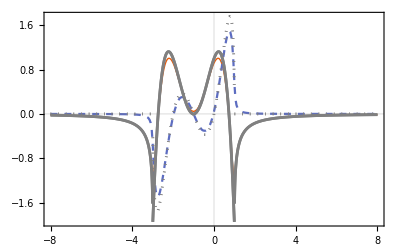

```mathematica
g=-1;t=-1;l=2;m=3;
ωMax=8;η=0.05;
greenNumerics=ListPlot[ParallelMap[ReIm@Gnumerics[l,m,#+ⅈ η]&,Range[-ωMax,ωMax,η]]ᵀ,DataRange->{-ωMax,ωMax},PlotTheme->"Scientific",Joined->True,PlotRange->All,PlotStyle->{Thick,Dashed}];
greenAnalytics=ReImPlot[{GanalyticsSqrt[l,m,ω],GanalyticsExp[l,m,ω]},{ω,-ωMax,ωMax},PlotStyle->{Gray},PlotRange->All];
Show[greenNumerics,greenAnalytics,PlotRange->All]
```

The above plot compares the real and imaginary parts of the Green’s function calculated numerically with those derived analytically, validating the consistency between the two methods.

## Edge Green’s Function for Self-Energy

Finally, we visualize the edge Green’s function, which is pivotal for determining the self-energy corrections, as indicated by Equation (S5) and applied in Equation (S10) of the Supplemental Material.

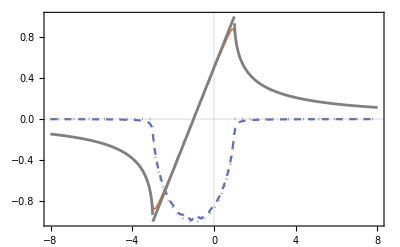

```mathematica
GanalyticsSurface[ω_]:=1/(2 t^2)(ω-g+Piecewise[{{-Sign[t] √((ω-g)^2-(2t)^2), (g-ω)/(2 t)<-1}, {-ⅈ √((2t)^2-(ω-g)^2), -1<=(g-ω)/(2 t)<=+1}, {+Sign[t] √((ω-g)^2-(2t)^2), (g-ω)/(2 t)>1}}]);
g=-1;t=-1;l=1;m=1;
ωMax=8;η=0.05;
greenNumerics=ListPlot[ParallelMap[ReIm@Gnumerics[l,m,#+ⅈ η]&,Range[-ωMax,ωMax,η]]ᵀ,DataRange->{-ωMax,ωMax},PlotTheme->"Scientific",Joined->True,PlotRange->All,PlotStyle->{Thick,Dashed}];
greenAnalytics=ReImPlot[GanalyticsSurface[ω],{ω,-ωMax,ωMax},PlotStyle->{Gray},PlotRange->All];
Show[greenNumerics,greenAnalytics,PlotRange->All]
```

The above plots demonstrate the excellent agreement between the analytical expression and the numerical results.

# Conclusion

In this notebook, we have explored the effects of dissipation on persistent currents in quantum many-body systems, using a newly introduced non-Hermitian Fermi-Dirac distribution. The combination of analytical derivations and numerical verifications presented here provides a robust framework for calculating persistent currents in non-Hermitian systems, particularly in phase-biased SNS junctions and normal mesoscopic rings. Our results confirm that quantum many-body observables in equilibrium remain continuous and exhibit no anomalies at exceptional points, underscoring the validity of the non-Hermitian approach. The notebook not only supports the findings of our Letter but also offers valuable tools for investigating non-Hermitian effects in both equilibrium and non-equilibrium quantum systems.